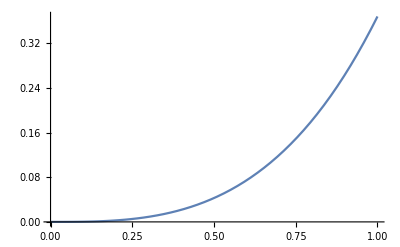

```mathematica
Plot[x Cosh[x]-Sinh[x],{x,0,1}]
```

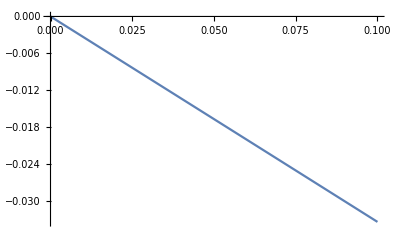

```mathematica
Plot[Sinh[x]/x^2-Cosh[x]/x,{x,0.00001,0.1}]
```

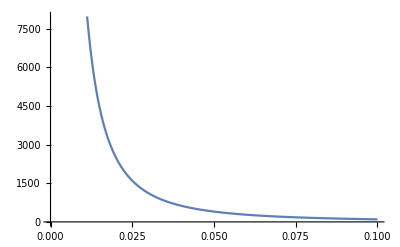

```mathematica
Plot[ⅇ^-x/x^2+ⅇ^-x/x,{x,0.00001,0.1}]
```

```mathematica
∫(ⅇ^-x/x^2+ⅇ^-x/x)ⅆx
```

-ⅇ^-x/x

```mathematica
∫(Sinh[x]/x^2-Cosh[x]/x)ⅆx
```

-Sinh[x]/x

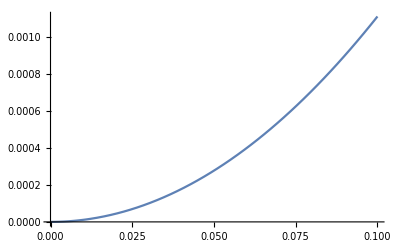

```mathematica
Plot[(Sinh[x]/x^2-Cosh[x]/x)^2,{x,0.00001,0.1}]
```

```mathematica
∫(ⅇ^-x/x^2+ⅇ^-x/x)^2 ⅆx
```

(ⅇ^(-2 x) (-1-2 x+x^2+2 ⅇ^(2 x) x^3 ExpIntegralEi[-2 x]))/(3 x^3)

```mathematica
∫(Sinh[x]/x^2-Cosh[x]/x)^2 ⅆx
```

(1-3 x^2+(-1+x^2) Cosh[2 x]+2 x Sinh[2 x]-2 x^3 SinhIntegral[2 x])/(6 x^3)

```mathematica
∫ⅇ^-x/x ⅆx
```

ExpIntegralEi[-x]

```mathematica
G=ⅇ^a/(1+a)(a Cosh[a]-Sinh[a]);
F=a^2/(1+a)ⅇ^a;
Expand[(H×G+F)^2(ⅇ^(-2 b)/2-ⅇ^(-2 a)/2+ⅇ^(-2 b)/b-ⅇ^(-2 a)/a)+H^2×(Cosh[2 b]/(2 b)-Cosh[2 a]/(2 a)+1/(2 a)-1/(2 b)+Sinh[2 a]/4-Sinh[2 b]/4+a/2-b/2)+2 H (H G+F)×((ⅇ^-b Sinh[b])/b-(ⅇ^-a Sinh[a])/a+b/2-a/2+ⅇ^(-2 a)/4-ⅇ^(-2 b)/4)]
```

-a^3/(1+a)^2-a^4/(2 (1+a)^2)+(a^4 ⅇ^(2 a-2 b))/(2 (1+a)^2)+(a^4 ⅇ^(2 a-2 b))/((1+a)^2 b)+(a^2 ⅇ^-a H)/(2 (1+a))-(a^3 ⅇ^a H)/(1+a)+(a^2 b ⅇ^a H)/(1+a)-(a^2 ⅇ^(a-2 b) H)/(2 (1+a))+H^2/(2 a)+(a H^2)/2-H^2/(2 b)-(b H^2)/2-(2 a^2 H Cosh[a])/(1+a)^2-(a^3 H Cosh[a])/(1+a)^2+(a^3 ⅇ^(2 a-2 b) H Cosh[a])/(1+a)^2+(2 a^3 ⅇ^(2 a-2 b) H Cosh[a])/((1+a)^2 b)+(a ⅇ^-a H^2 Cosh[a])/(2 (1+a))-(a^2 ⅇ^a H^2 Cosh[a])/(1+a)+(a b ⅇ^a H^2 Cosh[a])/(1+a)-(a ⅇ^(a-2 b) H^2 Cosh[a])/(2 (1+a))-(a H^2 Cosh[a]^2)/(1+a)^2-(a^2 H^2 Cosh[a]^2)/(2 (1+a)^2)+(a^2 ⅇ^(2 a-2 b) H^2 Cosh[a]^2)/(2 (1+a)^2)+(a^2 ⅇ^(2 a-2 b) H^2 Cosh[a]^2)/((1+a)^2 b)-(H^2 Cosh[2 a])/(2 a)+(H^2 Cosh[2 b])/(2 b)+(2 a H Sinh[a])/(1+a)^2+(a^2 H Sinh[a])/(1+a)^2-(2 a H Sinh[a])/(1+a)-(a^2 ⅇ^(2 a-2 b) H Sinh[a])/(1+a)^2-(2 a^2 ⅇ^(2 a-2 b) H Sinh[a])/((1+a)^2 b)-(ⅇ^-a H^2 Sinh[a])/(2 (1+a))+(a ⅇ^a H^2 Sinh[a])/(1+a)-(b ⅇ^a H^2 Sinh[a])/(1+a)+(ⅇ^(a-2 b) H^2 Sinh[a])/(2 (1+a))+(2 H^2 Cosh[a] Sinh[a])/(1+a)^2+(a H^2 Cosh[a] Sinh[a])/(1+a)^2-(2 H^2 Cosh[a] Sinh[a])/(1+a)-(a ⅇ^(2 a-2 b) H^2 Cosh[a] Sinh[a])/(1+a)^2-(2 a ⅇ^(2 a-2 b) H^2 Cosh[a] Sinh[a])/((1+a)^2 b)-(H^2 Sinh[a]^2)/(2 (1+a)^2)-(H^2 Sinh[a]^2)/(a (1+a)^2)+(2 H^2 Sinh[a]^2)/(a (1+a))+(ⅇ^(2 a-2 b) H^2 Sinh[a]^2)/(2 (1+a)^2)+(ⅇ^(2 a-2 b) H^2 Sinh[a]^2)/((1+a)^2 b)+1/4 H^2 Sinh[2 a]+(2 a^2 ⅇ^(a-b) H Sinh[b])/((1+a) b)+(2 a ⅇ^(a-b) H^2 Cosh[a] Sinh[b])/((1+a) b)-(2 ⅇ^(a-b) H^2 Sinh[a] Sinh[b])/((1+a) b)-1/4 H^2 Sinh[2 b]

```mathematica
FullSimplify[%7]
```

1/(8 (1+a)^2 b)ⅇ^(-2 b) (-(1+a)^2 (-2+b) ⅇ^(4 b) H^2+(2+b) ⅇ^(2 a) (2 a^2+(-1+a) ⅇ^a H)^2+4 ⅇ^(2 b) (-a^3 (2+a) b-a^2 (-2 (1+a)+(3+a (3+2 a)) b-2 (1+a) b^2) ⅇ^a H+(-1+a^2-a^3 b+(-1+a^2) b^2) ⅇ^(2 a) H^2))

```mathematica
Simplify[%3]
```

(ⅇ^(-2 b) (-2 b ⅇ^(2 b)+a ((2+b) ⅇ^(2 a)-b ⅇ^(2 b))) (a^2+a H Cosh[a]-H Sinh[a])^2)/(2 a (1+a)^2 b)

```mathematica
Plot[(Sinh[100 x]),{x,0,1}]
```

-Graphics-

```mathematica
Plot[(Cosh[100 x]),{x,0,1}]
```

-Graphics-

```mathematica
Plot[(Sinh[100 x]/(√(100 x))),{x,0.0001,1}]
```

-Graphics-

```mathematica
Plot[(ⅇ^(100 x)),{x,0,1}]
```

-Graphics-

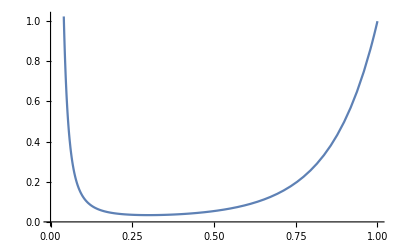

```mathematica
Plot[ⅇ^(10x)ⅇ^-10×1/x^3,{x,0.00001,1}]
```

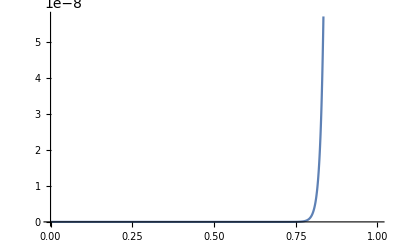

```mathematica
Plot[(Sinh[100 x] ⅇ^-100×1/x^3),{x,0.00001,1}]
```

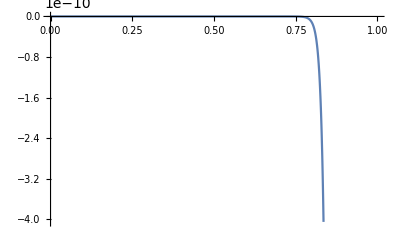

```mathematica
Plot[Sinh[100x]/(100x)^2 ⅇ^-100-Cosh[100 x]/(100x)ⅇ^-100,{x,0.00001,1}]
```

```mathematica
Collect[-a^3/(1+a)^2-a^4/(2 (1+a)^2)+(a^4 ⅇ^(2 a-2 b))/(2 (1+a)^2)+(a^4 ⅇ^(2 a-2 b))/((1+a)^2 b)+(a^2 ⅇ^-a H)/(2 (1+a))-(a^3 ⅇ^a H)/(1+a)+(a^2 b ⅇ^a H)/(1+a)-(a^2 ⅇ^(a-2 b) H)/(2 (1+a))+H^2/(2 a)+(a H^2)/2-H^2/(2 b)-(b H^2)/2-(2 a^2 H Cosh[a])/(1+a)^2-(a^3 H Cosh[a])/(1+a)^2+(a^3 ⅇ^(2 a-2 b) H Cosh[a])/(1+a)^2+(2 a^3 ⅇ^(2 a-2 b) H Cosh[a])/((1+a)^2 b)+(a ⅇ^-a H^2 Cosh[a])/(2 (1+a))-(a^2 ⅇ^a H^2 Cosh[a])/(1+a)+(a b ⅇ^a H^2 Cosh[a])/(1+a)-(a ⅇ^(a-2 b) H^2 Cosh[a])/(2 (1+a))-(a H^2 Cosh[a]^2)/(1+a)^2-(a^2 H^2 Cosh[a]^2)/(2 (1+a)^2)+(a^2 ⅇ^(2 a-2 b) H^2 Cosh[a]^2)/(2 (1+a)^2)+(a^2 ⅇ^(2 a-2 b) H^2 Cosh[a]^2)/((1+a)^2 b)-(H^2 Cosh[2 a])/(2 a)+(H^2 Cosh[2 b])/(2 b)+(2 a H Sinh[a])/(1+a)^2+(a^2 H Sinh[a])/(1+a)^2-(2 a H Sinh[a])/(1+a)-(a^2 ⅇ^(2 a-2 b) H Sinh[a])/(1+a)^2-(2 a^2 ⅇ^(2 a-2 b) H Sinh[a])/((1+a)^2 b)-(ⅇ^-a H^2 Sinh[a])/(2 (1+a))+(a ⅇ^a H^2 Sinh[a])/(1+a)-(b ⅇ^a H^2 Sinh[a])/(1+a)+(ⅇ^(a-2 b) H^2 Sinh[a])/(2 (1+a))+(2 H^2 Cosh[a] Sinh[a])/(1+a)^2+(a H^2 Cosh[a] Sinh[a])/(1+a)^2-(2 H^2 Cosh[a] Sinh[a])/(1+a)-(a ⅇ^(2 a-2 b) H^2 Cosh[a] Sinh[a])/(1+a)^2-(2 a ⅇ^(2 a-2 b) H^2 Cosh[a] Sinh[a])/((1+a)^2 b)-(H^2 Sinh[a]^2)/(2 (1+a)^2)-(H^2 Sinh[a]^2)/(a (1+a)^2)+(2 H^2 Sinh[a]^2)/(a (1+a))+(ⅇ^(2 a-2 b) H^2 Sinh[a]^2)/(2 (1+a)^2)+(ⅇ^(2 a-2 b) H^2 Sinh[a]^2)/((1+a)^2 b)+1/4 H^2 Sinh[2 a]+(2 a^2 ⅇ^(a-b) H Sinh[b])/((1+a) b)+(2 a ⅇ^(a-b) H^2 Cosh[a] Sinh[b])/((1+a) b)-(2 ⅇ^(a-b) H^2 Sinh[a] Sinh[b])/((1+a) b)-1/4 H^2 Sinh[2 b], H]
```

-a^3/(1+a)^2-a^4/(2 (1+a)^2)+(a^4 ⅇ^(2 a-2 b))/(2 (1+a)^2)+(a^4 ⅇ^(2 a-2 b))/((1+a)^2 b)+H ((a^2 ⅇ^-a)/(2 (1+a))-(a^3 ⅇ^a)/(1+a)+(a^2 b ⅇ^a)/(1+a)-(a^2 ⅇ^(a-2 b))/(2 (1+a))-(2 a^2 Cosh[a])/(1+a)^2-(a^3 Cosh[a])/(1+a)^2+(a^3 ⅇ^(2 a-2 b) Cosh[a])/(1+a)^2+(2 a^3 ⅇ^(2 a-2 b) Cosh[a])/((1+a)^2 b)+(2 a Sinh[a])/(1+a)^2+(a^2 Sinh[a])/(1+a)^2-(2 a Sinh[a])/(1+a)-(a^2 ⅇ^(2 a-2 b) Sinh[a])/(1+a)^2-(2 a^2 ⅇ^(2 a-2 b) Sinh[a])/((1+a)^2 b)+(2 a^2 ⅇ^(a-b) Sinh[b])/((1+a) b))+H^2 (1/(2 a)+a/2-1/(2 b)-b/2+(a ⅇ^-a Cosh[a])/(2 (1+a))-(a^2 ⅇ^a Cosh[a])/(1+a)+(a b ⅇ^a Cosh[a])/(1+a)-(a ⅇ^(a-2 b) Cosh[a])/(2 (1+a))-(a Cosh[a]^2)/(1+a)^2-(a^2 Cosh[a]^2)/(2 (1+a)^2)+(a^2 ⅇ^(2 a-2 b) Cosh[a]^2)/(2 (1+a)^2)+(a^2 ⅇ^(2 a-2 b) Cosh[a]^2)/((1+a)^2 b)-Cosh[2 a]/(2 a)+Cosh[2 b]/(2 b)-(ⅇ^-a Sinh[a])/(2 (1+a))+(a ⅇ^a Sinh[a])/(1+a)-(b ⅇ^a Sinh[a])/(1+a)+(ⅇ^(a-2 b) Sinh[a])/(2 (1+a))+(2 Cosh[a] Sinh[a])/(1+a)^2+(a Cosh[a] Sinh[a])/(1+a)^2-(2 Cosh[a] Sinh[a])/(1+a)-(a ⅇ^(2 a-2 b) Cosh[a] Sinh[a])/(1+a)^2-(2 a ⅇ^(2 a-2 b) Cosh[a] Sinh[a])/((1+a)^2 b)-Sinh[a]^2/(2 (1+a)^2)-Sinh[a]^2/(a (1+a)^2)+(2 Sinh[a]^2)/(a (1+a))+(ⅇ^(2 a-2 b) Sinh[a]^2)/(2 (1+a)^2)+(ⅇ^(2 a-2 b) Sinh[a]^2)/((1+a)^2 b)+1/4 Sinh[2 a]+(2 a ⅇ^(a-b) Cosh[a] Sinh[b])/((1+a) b)-(2 ⅇ^(a-b) Sinh[a] Sinh[b])/((1+a) b)-1/4 Sinh[2 b])

```mathematica
Simplify[%1]
```

1/(8 (1+a)^2 b)ⅇ^(-2 b) (-2 a ((2+b) ⅇ^(4 a)+(-2+b) ⅇ^(4 b)) H^2+((2+b) ⅇ^(4 a)-(-2+b) ⅇ^(4 b)-4 (1+b^2) ⅇ^(2 (a+b))) H^2+a^2 H (-4 (2+b) ⅇ^(3 a)+4 (2-3 b+2 b^2) ⅇ^(a+2 b)+(2+b) ⅇ^(4 a) H-(-2+b) ⅇ^(4 b) H+4 (1+b^2) ⅇ^(2 (a+b)) H)+4 a^4 ((2+b) ⅇ^(2 a)-b ⅇ^(2 b)-2 b ⅇ^(a+2 b) H)+4 a^3 (2 b^2 ⅇ^(a+2 b) H+2 ⅇ^a (ⅇ^(2 a)+ⅇ^(2 b)) H-b (2 ⅇ^(2 b)-ⅇ^(3 a) H+3 ⅇ^(a+2 b) H+ⅇ^(2 (a+b)) H^2)))

```mathematica
Simplify[1/(2 a)+a/2-1/(2 b)-b/2+(a ⅇ^-a Cosh[a])/(2 (1+a))-(a^2 ⅇ^a Cosh[a])/(1+a)+(a b ⅇ^a Cosh[a])/(1+a)-(a ⅇ^(a-2 b) Cosh[a])/(2 (1+a))-(a Cosh[a]^2)/(1+a)^2-(a^2 Cosh[a]^2)/(2 (1+a)^2)+(a^2 ⅇ^(2 a-2 b) Cosh[a]^2)/(2 (1+a)^2)+(a^2 ⅇ^(2 a-2 b) Cosh[a]^2)/((1+a)^2 b)-Cosh[2 a]/(2 a)+Cosh[2 b]/(2 b)-(ⅇ^-a Sinh[a])/(2 (1+a))+(a ⅇ^a Sinh[a])/(1+a)-(b ⅇ^a Sinh[a])/(1+a)+(ⅇ^(a-2 b) Sinh[a])/(2 (1+a))+(2 Cosh[a] Sinh[a])/(1+a)^2+(a Cosh[a] Sinh[a])/(1+a)^2-(2 Cosh[a] Sinh[a])/(1+a)-(a ⅇ^(2 a-2 b) Cosh[a] Sinh[a])/(1+a)^2-(2 a ⅇ^(2 a-2 b) Cosh[a] Sinh[a])/((1+a)^2 b)-Sinh[a]^2/(2 (1+a)^2)-Sinh[a]^2/(a (1+a)^2)+(2 Sinh[a]^2)/(a (1+a))+(ⅇ^(2 a-2 b) Sinh[a]^2)/(2 (1+a)^2)+(ⅇ^(2 a-2 b) Sinh[a]^2)/((1+a)^2 b)+1/4 Sinh[2 a]+(2 a ⅇ^(a-b) Cosh[a] Sinh[b])/((1+a) b)-(2 ⅇ^(a-b) Sinh[a] Sinh[b])/((1+a) b)-1/4 Sinh[2 b]]
```

(ⅇ^(-2 b) ((-1+a)^2 (2+b) ⅇ^(4 a)-(1+a)^2 (-2+b) ⅇ^(4 b)-4 (1+a^3 b+b^2-a^2 (1+b^2)) ⅇ^(2 (a+b))))/(8 (1+a)^2 b)

```mathematica
Simplify[(a^2 ⅇ^-a)/(2 (1+a))-(a^3 ⅇ^a)/(1+a)+(a^2 b ⅇ^a)/(1+a)-(a^2 ⅇ^(a-2 b))/(2 (1+a))-(2 a^2 Cosh[a])/(1+a)^2-(a^3 Cosh[a])/(1+a)^2+(a^3 ⅇ^(2 a-2 b) Cosh[a])/(1+a)^2+(2 a^3 ⅇ^(2 a-2 b) Cosh[a])/((1+a)^2 b)+(2 a Sinh[a])/(1+a)^2+(a^2 Sinh[a])/(1+a)^2-(2 a Sinh[a])/(1+a)-(a^2 ⅇ^(2 a-2 b) Sinh[a])/(1+a)^2-(2 a^2 ⅇ^(2 a-2 b) Sinh[a])/((1+a)^2 b)+(2 a^2 ⅇ^(a-b) Sinh[b])/((1+a) b)]
```

(a^2 ⅇ^(a-2 b) ((-1+a) (2+b) ⅇ^(2 a)+(2-3 b-2 a^2 b+2 b^2+a (2-3 b+2 b^2)) ⅇ^(2 b)))/(2 (1+a)^2 b)

```mathematica
Simplify[-a^3/(1+a)^2-a^4/(2 (1+a)^2)+(a^4 ⅇ^(2 a-2 b))/(2 (1+a)^2)+(a^4 ⅇ^(2 a-2 b))/((1+a)^2 b)]
```

(a^3 ⅇ^(-2 b) (-2 b ⅇ^(2 b)+a ((2+b) ⅇ^(2 a)-b ⅇ^(2 b))))/(2 (1+a)^2 b)

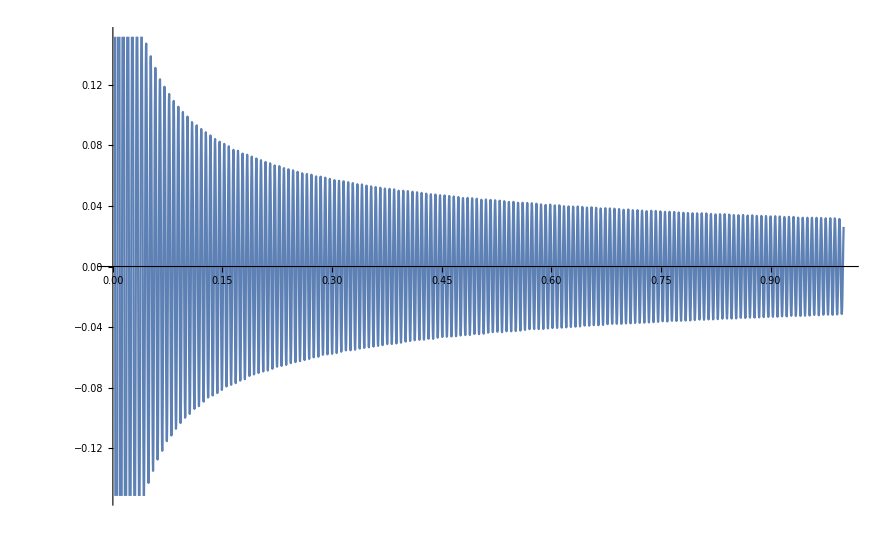

```mathematica
Plot[(Sin[1000 x]/(√(1000 x))),{x,0.0001,1}]
```

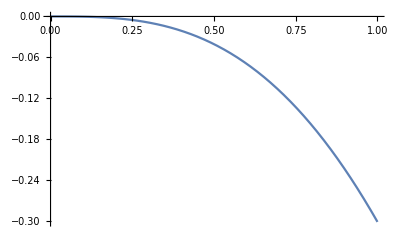

```mathematica
Plot[x Cos[x]-Sin[x],{x,0,1}]
```

```mathematica
y[x_]:=C×√(2/(π×x))×Sin[x]+D×√(2/(π×x))×Cos[x];
Expand[-1/2×x^(-3/2)×y[x]+x^(-1/2)×y'[x]]
```

-(D √(2/π) √(1/x) Cos[x])/x^(3/2)+(C √(2/π) √(1/x) Cos[x])/(√x)-(C √(2/π) √(1/x) Sin[x])/x^(3/2)-(D √(2/π) √(1/x) Sin[x])/(√x)

```mathematica
Simplify[-(D √(2/π) √(1/x) Cos[x])/x^(3/2)+(C √(2/π) √(1/x) Cos[x])/(√x)-(C √(2/π) √(1/x) Sin[x])/x^(3/2)-(D √(2/π) √(1/x) Sin[x])/(√x)]
```

-(√(2/π) √(1/x) ((D-C x) Cos[x]+(C+D x) Sin[x]))/x^(3/2)

```mathematica
Solve[(d-c a)×Cos[a]+(c+d a)×Sin[a]==a^2, d]
```

{{d→(a^2+a c Cos[a]-c Sin[a])/(Cos[a]+a Sin[a])}}

```mathematica
Solve[(d-c a)×Cos[a]+(c+d a)×Sin[a]==a^2, c]
```

{{c→(-a^2+d Cos[a]+a d Sin[a])/(a Cos[a]-Sin[a])}}

```mathematica
d=(a^2+a c Cos[a]-c Sin[a])/(Cos[a]+a Sin[a]);
Expand[((d-c x)×Cos[x]+(c+d x)×Sin[x])/x^2]
```

-(c Cos[x])/x+(a^2 Cos[x])/(x^2 (Cos[a]+a Sin[a]))+(a c Cos[a] Cos[x])/(x^2 (Cos[a]+a Sin[a]))-(c Cos[x] Sin[a])/(x^2 (Cos[a]+a Sin[a]))+(c Sin[x])/x^2+(a^2 Sin[x])/(x (Cos[a]+a Sin[a]))+(a c Cos[a] Sin[x])/(x (Cos[a]+a Sin[a]))-(c Sin[a] Sin[x])/(x (Cos[a]+a Sin[a]))

```mathematica
Simplify[%10]
```

(Global`c (Global`a-Global`x) Cos[Global`a-Global`x]+(Global`a)^2 Cos[Global`x]-Global`c Sin[Global`a-Global`x]-Global`a Global`c Global`x Sin[Global`a-Global`x]+(Global`a)^2 Global`x Sin[Global`x])/((Global`x)^2 (Cos[Global`a]+Global`a Sin[Global`a]))

```mathematica
Manipulate[Plot[%10,{Global`x,-8,8}],{Global`a,0,100},{Global`c,-2,2}]
```

```mathematica
Simplify[-(c Cos[x])/x+(a^2 Cos[x])/(x^2 (Cos[a]+a Sin[a]))+(a c Cos[a] Cos[x])/(x^2 (Cos[a]+a Sin[a]))-(c Cos[x] Sin[a])/(x^2 (Cos[a]+a Sin[a]))+(c Sin[x])/x^2+(a^2 Sin[x])/(x (Cos[a]+a Sin[a]))+(a c Cos[a] Sin[x])/(x (Cos[a]+a Sin[a]))-(c Sin[a] Sin[x])/(x (Cos[a]+a Sin[a]))]
```

(c (a-x) Cos[a-x]+a^2 Cos[x]-c Sin[a-x]-a c x Sin[a-x]+a^2 x Sin[x])/(x^2 (Cos[a]+a Sin[a]))

```mathematica
Collect[-(c Cos[x])/x+(a^2 Cos[x])/(x^2 (Cos[a]+a Sin[a]))+(a c Cos[a] Cos[x])/(x^2 (Cos[a]+a Sin[a]))-(c Cos[x] Sin[a])/(x^2 (Cos[a]+a Sin[a]))+(c Sin[x])/x^2+(a^2 Sin[x])/(x (Cos[a]+a Sin[a]))+(a c Cos[a] Sin[x])/(x (Cos[a]+a Sin[a]))-(c Sin[a] Sin[x])/(x (Cos[a]+a Sin[a])),c]
```

(a^2 Cos[x])/(x^2 (Cos[a]+a Sin[a]))+(a^2 Sin[x])/(x (Cos[a]+a Sin[a]))+c (-Cos[x]/x+(a Cos[a] Cos[x])/(x^2 (Cos[a]+a Sin[a]))-(Cos[x] Sin[a])/(x^2 (Cos[a]+a Sin[a]))+Sin[x]/x^2+(a Cos[a] Sin[x])/(x (Cos[a]+a Sin[a]))-(Sin[a] Sin[x])/(x (Cos[a]+a Sin[a])))

```mathematica
Simplify[(a^2 Cos[x])/(x^2 (Cos[a]+a Sin[a]))+(a^2 Sin[x])/(x (Cos[a]+a Sin[a]))]
```

(a^2 (Cos[x]+x Sin[x]))/(x^2 (Cos[a]+a Sin[a]))

```mathematica
Simplify[-Cos[x]/x+(a Cos[a] Cos[x])/(x^2 (Cos[a]+a Sin[a]))-(Cos[x] Sin[a])/(x^2 (Cos[a]+a Sin[a]))+Sin[x]/x^2+(a Cos[a] Sin[x])/(x (Cos[a]+a Sin[a]))-(Sin[a] Sin[x])/(x (Cos[a]+a Sin[a]))]
```

((a-x) Cos[a-x]-(1+a x) Sin[a-x])/(x^2 (Cos[a]+a Sin[a]))

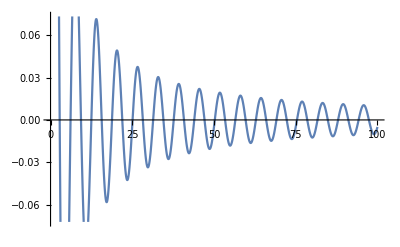

```mathematica
Plot[(Cos[x]+x Sin[x])/x^2,{x,0.0001,100}]
```

```mathematica
Expand[(a-x) Cos[a-x]-(1+a x) Sin[a-x]]
```

a Cos[a-x]-x Cos[a-x]-Sin[a-x]-a x Sin[a-x]

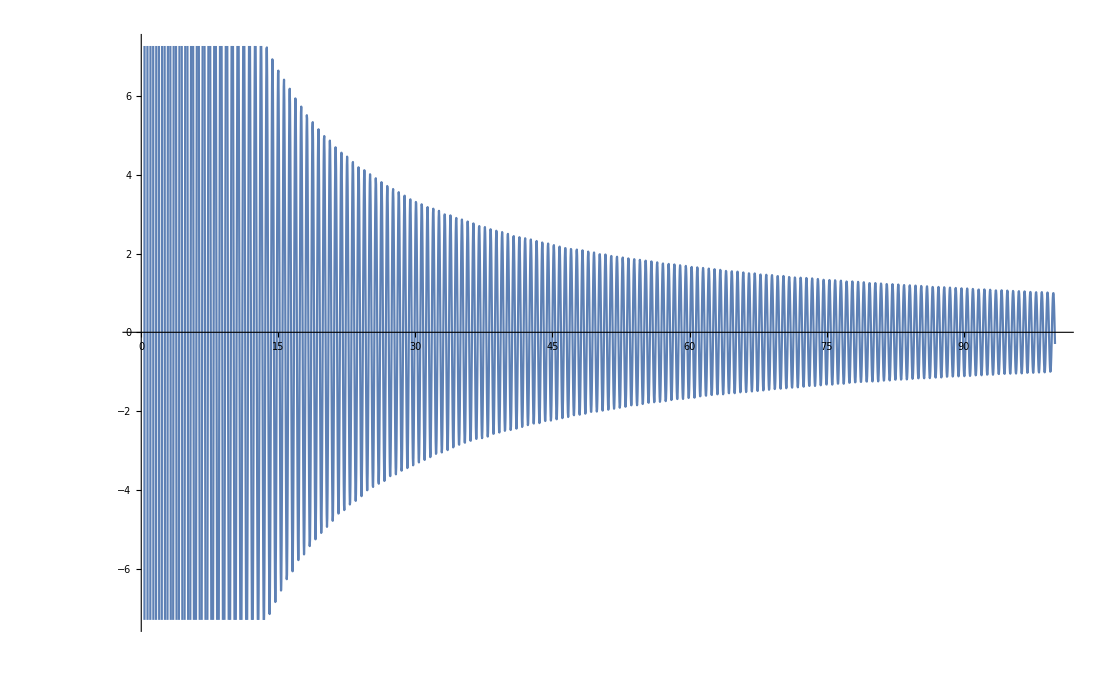

```mathematica
Plot[(10(1-x) Cos[10×(1-x)]-(1+10^2 x) Sin[10×(1-x)])/(x)^2,{x,0.0001,100}]
```

```mathematica
∫(F/A×((a-x)Cos[a-x]-(1+a x)Sin[a-x])/x^2+1/A×a^2/x^2×(Cos[x]+x Sin[x]))^2×x^2 ⅆx
```

1/(4 A^2 x)(-2 a^4-2 F^2-2 a^2 F^2+2 a^4 x^2+2 F^2 x^2+2 a^2 F^2 x^2+4 a^3 F (-1+x^2) Cos[a]+2 a^2 F (-2 a+x) Cos[a-2 x]+2 F^2 Cos[2 (a-x)]-2 a^2 F^2 Cos[2 (a-x)]+2 a F^2 x Cos[2 (a-x)]-2 a^4 Cos[2 x]+4 a^2 F Sin[a]-4 a^2 F x^2 Sin[a]+4 a^2 F Sin[a-2 x]+2 a^3 F x Sin[a-2 x]+4 a F^2 Sin[2 (a-x)]-F^2 x Sin[2 (a-x)]+a^2 F^2 x Sin[2 (a-x)]-a^4 x Sin[2 x])

```mathematica
Simplify[%6]
```

1/(4 A^2 x)(-2 a^4-2 F^2-2 a^2 F^2+2 a^4 x^2+2 F^2 x^2+2 a^2 F^2 x^2+4 a^3 F (-1+x^2) Cos[a]+2 a^2 F (-2 a+x) Cos[a-2 x]+2 F^2 Cos[2 (a-x)]-2 a^2 F^2 Cos[2 (a-x)]+2 a F^2 x Cos[2 (a-x)]-2 a^4 Cos[2 x]+4 a^2 F Sin[a]-4 a^2 F x^2 Sin[a]+4 a^2 F Sin[a-2 x]+2 a^3 F x Sin[a-2 x]+4 a F^2 Sin[2 (a-x)]-F^2 x Sin[2 (a-x)]+a^2 F^2 x Sin[2 (a-x)]-a^4 x Sin[2 x])

```mathematica
∫_b^a (F/A×((a-x)Cos[a-x]-(1+a x)Sin[a-x])/x^2+1/A×a^2/x^2×(Cos[x]+x Sin[x]))^2×x^2 ⅆx
```

ConditionalExpression[1/A^2(1/4 a^2 (2 (-3+2 a^2) F Cos[a]+2 a (-1+a^2+F^2-Cos[2 a]-(3 F+a Cos[a]) Sin[a]))-1/(4 b)(-2 a^4+2 a^4 b^2-2 F^2-2 a^2 F^2+2 b^2 F^2+2 a^2 b^2 F^2+4 a^3 (-1+b^2) F Cos[a]-2 a^2 (2 a-b) F Cos[a-2 b]+2 F^2 Cos[2 a-2 b]-2 a^2 F^2 Cos[2 a-2 b]+2 a b F^2 Cos[2 a-2 b]-2 a^4 Cos[2 b]+4 a^2 F Sin[a]-4 a^2 b^2 F Sin[a]+4 a^2 F Sin[a-2 b]+2 a^3 b F Sin[a-2 b]+4 a F^2 Sin[2 a-2 b]-b F^2 Sin[2 a-2 b]+a^2 b F^2 Sin[2 a-2 b]-a^4 b Sin[2 b])),(b≠0&&a b≠b^2&&Re[b/(a-b)]≥0)||Re[b/(a-b)]<-1||b/(a-b)∉Reals]

```mathematica
Simplify[1/A^2(1/4 a^2 (2 (-3+2 a^2) F Cos[a]+2 a (-1+a^2+F^2-Cos[2 a]-(3 F+a Cos[a]) Sin[a]))-1/(4 b)(-2 a^4+2 a^4 b^2-2 F^2-2 a^2 F^2+2 b^2 F^2+2 a^2 b^2 F^2+4 a^3 (-1+b^2) F Cos[a]-2 a^2 (2 a-b) F Cos[a-2 b]+2 F^2 Cos[2 a-2 b]-2 a^2 F^2 Cos[2 a-2 b]+2 a b F^2 Cos[2 a-2 b]-2 a^4 Cos[2 b]+4 a^2 F Sin[a]-4 a^2 b^2 F Sin[a]+4 a^2 F Sin[a-2 b]+2 a^3 b F Sin[a-2 b]+4 a F^2 Sin[2 a-2 b]-b F^2 Sin[2 a-2 b]+a^2 b F^2 Sin[2 a-2 b]-a^4 b Sin[2 b]))]
```

1/(4 A^2)(a^2 (2 (-3+2 a^2) F Cos[a]+2 a (-1+a^2+F^2-Cos[2 a]-(3 F+a Cos[a]) Sin[a]))+1/b(2 a^4-2 a^4 b^2+2 F^2+2 a^2 F^2-2 b^2 F^2-2 a^2 b^2 F^2-4 a^3 (-1+b^2) F Cos[a]+2 a^2 (2 a-b) F Cos[a-2 b]-2 F^2 Cos[2 (a-b)]+2 a^2 F^2 Cos[2 (a-b)]-2 a b F^2 Cos[2 (a-b)]+2 a^4 Cos[2 b]-4 a^2 F Sin[a]+4 a^2 b^2 F Sin[a]-4 a^2 F Sin[a-2 b]-2 a^3 b F Sin[a-2 b]-4 a F^2 Sin[2 (a-b)]+b F^2 Sin[2 (a-b)]-a^2 b F^2 Sin[2 (a-b)]+a^4 b Sin[2 b]))

```mathematica
Collect[1/A^2(1/4 a^2 (2 (-3+2 a^2) F Cos[a]+2 a (-1+a^2+F^2-Cos[2 a]-(3 F+a Cos[a]) Sin[a]))-1/(4 b)(-2 a^4+2 a^4 b^2-2 F^2-2 a^2 F^2+2 b^2 F^2+2 a^2 b^2 F^2+4 a^3 (-1+b^2) F Cos[a]-2 a^2 (2 a-b) F Cos[a-2 b]+2 F^2 Cos[2 a-2 b]-2 a^2 F^2 Cos[2 a-2 b]+2 a b F^2 Cos[2 a-2 b]-2 a^4 Cos[2 b]+4 a^2 F Sin[a]-4 a^2 b^2 F Sin[a]+4 a^2 F Sin[a-2 b]+2 a^3 b F Sin[a-2 b]+4 a F^2 Sin[2 a-2 b]-b F^2 Sin[2 a-2 b]+a^2 b F^2 Sin[2 a-2 b]-a^4 b Sin[2 b])), F]
```

(F (1/2 a^2 (-3+2 a^2) Cos[a]-(a^3 (-1+b^2) Cos[a])/b+(a^2 (2 a-b) Cos[a-2 b])/(2 b)-3/2 a^3 Sin[a]-(a^2 Sin[a])/b+a^2 b Sin[a]-1/2 a^3 Sin[a-2 b]-(a^2 Sin[a-2 b])/b))/A^2+(F^2 (a^3/2+1/(2 b)+a^2/(2 b)-b/2-(a^2 b)/2-1/2 a Cos[2 a-2 b]-Cos[2 a-2 b]/(2 b)+(a^2 Cos[2 a-2 b])/(2 b)+1/4 Sin[2 a-2 b]-1/4 a^2 Sin[2 a-2 b]-(a Sin[2 a-2 b])/b))/A^2+(-a^3/2+a^5/2+a^4/(2 b)-(a^4 b)/2-1/2 a^3 Cos[2 a]+(a^4 Cos[2 b])/(2 b)-1/2 a^4 Cos[a] Sin[a]+1/4 a^4 Sin[2 b])/A^2

```mathematica
Simplify[a^3/2+1/(2 b)+a^2/(2 b)-b/2-(a^2 b)/2-1/2 a Cos[2 a-2 b]-Cos[2 a-2 b]/(2 b)+(a^2 Cos[2 a-2 b])/(2 b)+1/4 Sin[2 a-2 b]-1/4 a^2 Sin[2 a-2 b]-(a Sin[2 a-2 b])/b]
```

(2 (1+a^2+a^3 b-b^2-a^2 b^2)+2 (-1+a^2-a b) Cos[2 (a-b)]+(-4 a+b-a^2 b) Sin[2 (a-b)])/(4 b)

```mathematica
FullSimplify[1/2 a^2 (-3+2 a^2) Cos[a]-(a^3 (-1+b^2) Cos[a])/b+(a^2 (2 a-b) Cos[a-2 b])/(2 b)-3/2 a^3 Sin[a]-(a^2 Sin[a])/b+a^2 b Sin[a]-1/2 a^3 Sin[a-2 b]-(a^2 Sin[a-2 b])/b]
```

(a^2 ((-3 b+2 a (1+(a-b) b)) Cos[a]+(2 a-b) Cos[a-2 b]+(-2-3 a b+2 b^2) Sin[a]-(2+a b) Sin[a-2 b]))/(2 b)

```mathematica
FullSimplify[-a^3/2+a^5/2+a^4/(2 b)-(a^4 b)/2-1/2 a^3 Cos[2 a]+(a^4 Cos[2 b])/(2 b)-1/2 a^4 Cos[a] Sin[a]+1/4 a^4 Sin[2 b]]
```

(a^3 (2 (a-b) (1+a b)-2 b Cos[2 a]+2 a Cos[2 b]+a b (-Sin[2 a]+Sin[2 b])))/(4 b)

```mathematica
E2=(a (1-t) Cos[a (1-t)]-(1+a^2 t)Sin[a (1-t)])/(t^2 a^2(Cos[a]+a Sin[a]));
∫ⅇ^(ⅈ w t)t^2 E2^2 ⅆt
```

1/(8 a^4 (Cos[a]+a Sin[a])^2)((ⅈ a^2 ⅇ^(-2 ⅈ a (1+t)+ⅈ t w) (-1+ⅇ^(4 ⅈ a)) (2 a (1+ⅇ^(4 ⅈ a t))+w-ⅇ^(4 ⅈ a t) w))/(4 a^2-w^2)-(ⅈ a^4 ⅇ^(-2 ⅈ a (1+t)+ⅈ t w) (-1+ⅇ^(4 ⅈ a)) (2 a (1+ⅇ^(4 ⅈ a t))+w-ⅇ^(4 ⅈ a t) w))/(4 a^2-w^2)+(2 a^3 ⅇ^(-2 ⅈ a (1+t)+ⅈ t w) (1+ⅇ^(4 ⅈ a)) (2 a (1+ⅇ^(4 ⅈ a t))+w-ⅇ^(4 ⅈ a t) w))/(4 a^2-w^2)+2 a^3 ⅇ^(-2 ⅈ a (1+t)+ⅈ t w) (-1+ⅇ^(4 ⅈ a)) (1/(2 a-w)-ⅇ^(4 ⅈ a t)/(2 a+w))+ⅈ a^2 ⅇ^(-2 ⅈ a (1+t)+ⅈ t w) (1+ⅇ^(4 ⅈ a)) (1/(2 a-w)-ⅇ^(4 ⅈ a t)/(2 a+w))-ⅈ a^4 ⅇ^(-2 ⅈ a (1+t)+ⅈ t w) (1+ⅇ^(4 ⅈ a)) (1/(2 a-w)-ⅇ^(4 ⅈ a t)/(2 a+w))-2 Cos[2 a] (-ⅇ^(-ⅈ t (2 a-w))/t-ⅇ^(ⅈ t (2 a+w))/t+ⅈ (2 a+w) ExpIntegralEi[ⅈ t (2 a+w)]-ⅈ (2 a-w) ExpIntegralEi[-2 ⅈ a t+ⅈ t w])+2 a^2 Cos[2 a] (-ⅇ^(-ⅈ t (2 a-w))/t-ⅇ^(ⅈ t (2 a+w))/t+ⅈ (2 a+w) ExpIntegralEi[ⅈ t (2 a+w)]-ⅈ (2 a-w) ExpIntegralEi[-2 ⅈ a t+ⅈ t w])-(4 Cos[a] (t (2 a+w) ExpIntegralEi[ⅈ t (2 a+w)]+ⅇ^(-ⅈ t (2 a-w)) (ⅈ (-1+ⅇ^(4 ⅈ a t))+ⅇ^(ⅈ t (2 a-w)) t (2 a-w) ExpIntegralEi[-2 ⅈ a t+ⅈ t w])) Sin[a])/t+1/t 4 a (t (2 a+w) ExpIntegralEi[ⅈ t (2 a+w)]+ⅇ^(-ⅈ t (2 a-w)) (ⅈ (-1+ⅇ^(4 ⅈ a t))+ⅇ^(ⅈ t (2 a-w)) t (2 a-w) ExpIntegralEi[-2 ⅈ a t+ⅈ t w])) (Cos[a]-Sin[a]) (Cos[a]+Sin[a])-1/(t w)4 ⅈ (-(1+a^2) t w^2 ExpIntegralEi[ⅈ t w]+(ⅈ+a) ((-ⅈ+a) ⅇ^(ⅈ t w) (a^2 t-ⅈ w)-a (ⅈ+a) t w ExpIntegralEi[-2 ⅈ a t+ⅈ t w] (Cos[2 a]+ⅈ Sin[2 a]))+a (-ⅈ+a)^2 t w ExpIntegralEi[ⅈ t (2 a+w)] (Cos[2 a]-ⅈ Sin[2 a]))-4 a (-ⅇ^(-ⅈ t (2 a-w))/t-ⅇ^(ⅈ t (2 a+w))/t+ⅈ (2 a+w) ExpIntegralEi[ⅈ t (2 a+w)]-ⅈ (2 a-w) ExpIntegralEi[-2 ⅈ a t+ⅈ t w]) Sin[2 a]+(2 a^2 (t (2 a+w) ExpIntegralEi[ⅈ t (2 a+w)]+ⅇ^(-ⅈ t (2 a-w)) (ⅈ (-1+ⅇ^(4 ⅈ a t))+ⅇ^(ⅈ t (2 a-w)) t (2 a-w) ExpIntegralEi[-2 ⅈ a t+ⅈ t w])) Sin[2 a])/t)

```mathematica
∫_b^1 ⅇ^(ⅈ w t)t^2 E2^2 ⅆt
```

ConditionalExpression[1/(4 a^4 b w (-4 a^2+w^2) (Cos[a]+a Sin[a])^2)ⅇ^(-2 ⅈ a (1+b)) (8 ⅈ a^4 b ⅇ^(ⅈ (2 a (1+b)+w))+8 ⅈ a^6 b ⅇ^(ⅈ (2 a (1+b)+w))-8 ⅈ a^4 b ⅇ^(ⅈ (2 a (1+b)+b w))-8 ⅈ a^6 b ⅇ^(ⅈ (2 a (1+b)+b w))+4 a^2 ⅇ^(ⅈ b (4 a+w)) w+8 ⅈ a^3 ⅇ^(ⅈ b (4 a+w)) w-4 a^4 ⅇ^(ⅈ b (4 a+w)) w-2 ⅈ a^3 b ⅇ^(ⅈ b (4 a+w)) w+4 a^4 b ⅇ^(ⅈ b (4 a+w)) w+2 ⅈ a^5 b ⅇ^(ⅈ b (4 a+w)) w+8 a^4 b ⅇ^(ⅈ (2 a (1+b)+w)) w+4 a^2 ⅇ^(ⅈ (4 a+b w)) w-8 ⅈ a^3 ⅇ^(ⅈ (4 a+b w)) w-4 a^4 ⅇ^(ⅈ (4 a+b w)) w+2 ⅈ a^3 b ⅇ^(ⅈ (4 a+b w)) w+4 a^4 b ⅇ^(ⅈ (4 a+b w)) w-2 ⅈ a^5 b ⅇ^(ⅈ (4 a+b w)) w-8 a^2 ⅇ^(ⅈ (2 a (1+b)+b w)) w-8 a^4 ⅇ^(ⅈ (2 a (1+b)+b w)) w+ⅈ a^2 b ⅇ^(ⅈ b (4 a+w)) w^2-2 a^3 b ⅇ^(ⅈ b (4 a+w)) w^2-ⅈ a^4 b ⅇ^(ⅈ b (4 a+w)) w^2-4 ⅈ a^2 b ⅇ^(ⅈ (2 a (1+b)+w)) w^2+ⅈ a^2 b ⅇ^(ⅈ (4 a+b w)) w^2+2 a^3 b ⅇ^(ⅈ (4 a+b w)) w^2-ⅈ a^4 b ⅇ^(ⅈ (4 a+b w)) w^2+2 ⅈ a^2 b ⅇ^(ⅈ (2 a (1+b)+b w)) w^2+2 ⅈ a^4 b ⅇ^(ⅈ (2 a (1+b)+b w)) w^2-ⅇ^(ⅈ b (4 a+w)) w^3-2 ⅈ a ⅇ^(ⅈ b (4 a+w)) w^3+a^2 ⅇ^(ⅈ b (4 a+w)) w^3-4 a^2 b ⅇ^(ⅈ (2 a (1+b)+w)) w^3-ⅇ^(ⅈ (4 a+b w)) w^3+2 ⅈ a ⅇ^(ⅈ (4 a+b w)) w^3+a^2 ⅇ^(ⅈ (4 a+b w)) w^3+2 ⅇ^(ⅈ (2 a (1+b)+b w)) w^3+2 a^2 ⅇ^(ⅈ (2 a (1+b)+b w)) w^3-2 ⅈ (1+a^2) b ⅇ^(2 ⅈ a (1+b)) w^2 (4 a^2-w^2) CosIntegral[w]+2 ⅈ (1+a^2) b ⅇ^(2 ⅈ a (1+b)) w^2 (4 a^2-w^2) CosIntegral[b w]+4 ⅈ a^2 b ⅇ^(2 ⅈ a b) w^2 CosIntegral[2 a+w]-8 a^3 b ⅇ^(2 ⅈ a b) w^2 CosIntegral[2 a+w]-4 ⅈ a^4 b ⅇ^(2 ⅈ a b) w^2 CosIntegral[2 a+w]-ⅈ b ⅇ^(2 ⅈ a b) w^4 CosIntegral[2 a+w]+2 a b ⅇ^(2 ⅈ a b) w^4 CosIntegral[2 a+w]+ⅈ a^2 b ⅇ^(2 ⅈ a b) w^4 CosIntegral[2 a+w]-4 ⅈ a^2 b ⅇ^(2 ⅈ a b) w^2 CosIntegral[b (2 a+w)]+8 a^3 b ⅇ^(2 ⅈ a b) w^2 CosIntegral[b (2 a+w)]+4 ⅈ a^4 b ⅇ^(2 ⅈ a b) w^2 CosIntegral[b (2 a+w)]+ⅈ b ⅇ^(2 ⅈ a b) w^4 CosIntegral[b (2 a+w)]-2 a b ⅇ^(2 ⅈ a b) w^4 CosIntegral[b (2 a+w)]-ⅈ a^2 b ⅇ^(2 ⅈ a b) w^4 CosIntegral[b (2 a+w)]+4 ⅈ a^2 b ⅇ^(2 ⅈ a (2+b)) w^2 ExpIntegralEi[-2 ⅈ a+ⅈ w]+8 a^3 b ⅇ^(2 ⅈ a (2+b)) w^2 ExpIntegralEi[-2 ⅈ a+ⅈ w]-4 ⅈ a^4 b ⅇ^(2 ⅈ a (2+b)) w^2 ExpIntegralEi[-2 ⅈ a+ⅈ w]-ⅈ b ⅇ^(2 ⅈ a (2+b)) w^4 ExpIntegralEi[-2 ⅈ a+ⅈ w]-2 a b ⅇ^(2 ⅈ a (2+b)) w^4 ExpIntegralEi[-2 ⅈ a+ⅈ w]+ⅈ a^2 b ⅇ^(2 ⅈ a (2+b)) w^4 ExpIntegralEi[-2 ⅈ a+ⅈ w]-4 ⅈ a^2 b ⅇ^(2 ⅈ a (2+b)) w^2 ExpIntegralEi[-2 ⅈ a b+ⅈ b w]-8 a^3 b ⅇ^(2 ⅈ a (2+b)) w^2 ExpIntegralEi[-2 ⅈ a b+ⅈ b w]+4 ⅈ a^4 b ⅇ^(2 ⅈ a (2+b)) w^2 ExpIntegralEi[-2 ⅈ a b+ⅈ b w]+ⅈ b ⅇ^(2 ⅈ a (2+b)) w^4 ExpIntegralEi[-2 ⅈ a b+ⅈ b w]+2 a b ⅇ^(2 ⅈ a (2+b)) w^4 ExpIntegralEi[-2 ⅈ a b+ⅈ b w]-ⅈ a^2 b ⅇ^(2 ⅈ a (2+b)) w^4 ExpIntegralEi[-2 ⅈ a b+ⅈ b w]+8 a^2 b ⅇ^(2 ⅈ a (1+b)) w^2 SinIntegral[w]+8 a^4 b ⅇ^(2 ⅈ a (1+b)) w^2 SinIntegral[w]-2 b ⅇ^(2 ⅈ a (1+b)) w^4 SinIntegral[w]-2 a^2 b ⅇ^(2 ⅈ a (1+b)) w^4 SinIntegral[w]-8 a^2 b ⅇ^(2 ⅈ a (1+b)) w^2 SinIntegral[b w]-8 a^4 b ⅇ^(2 ⅈ a (1+b)) w^2 SinIntegral[b w]+2 b ⅇ^(2 ⅈ a (1+b)) w^4 SinIntegral[b w]+2 a^2 b ⅇ^(2 ⅈ a (1+b)) w^4 SinIntegral[b w]-4 a^2 b ⅇ^(2 ⅈ a b) w^2 SinIntegral[2 a+w]-8 ⅈ a^3 b ⅇ^(2 ⅈ a b) w^2 SinIntegral[2 a+w]+4 a^4 b ⅇ^(2 ⅈ a b) w^2 SinIntegral[2 a+w]+b ⅇ^(2 ⅈ a b) w^4 SinIntegral[2 a+w]+2 ⅈ a b ⅇ^(2 ⅈ a b) w^4 SinIntegral[2 a+w]-a^2 b ⅇ^(2 ⅈ a b) w^4 SinIntegral[2 a+w]+4 a^2 b ⅇ^(2 ⅈ a b) w^2 SinIntegral[b (2 a+w)]+8 ⅈ a^3 b ⅇ^(2 ⅈ a b) w^2 SinIntegral[b (2 a+w)]-4 a^4 b ⅇ^(2 ⅈ a b) w^2 SinIntegral[b (2 a+w)]-b ⅇ^(2 ⅈ a b) w^4 SinIntegral[b (2 a+w)]-2 ⅈ a b ⅇ^(2 ⅈ a b) w^4 SinIntegral[b (2 a+w)]+a^2 b ⅇ^(2 ⅈ a b) w^4 SinIntegral[b (2 a+w)]),0<Re[b]<1&&Im[b]==0]

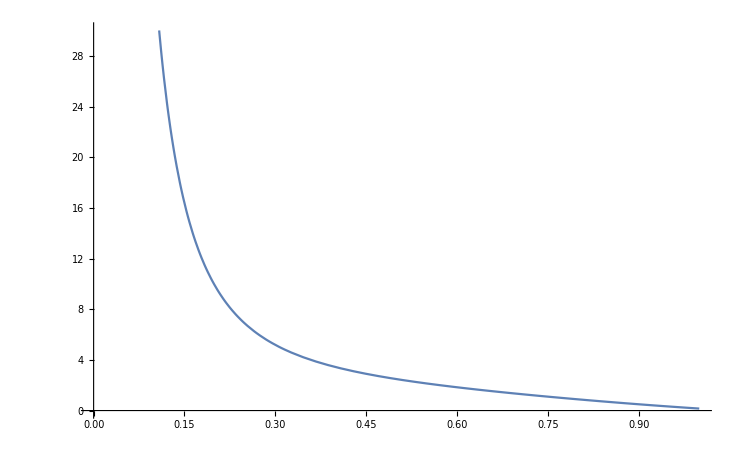

```mathematica
a=3;
Plot[(a (1-t )Cos[a t]+(1+a^2 t)Sin[a t])/(a t)^2,{t,0,1}]
```

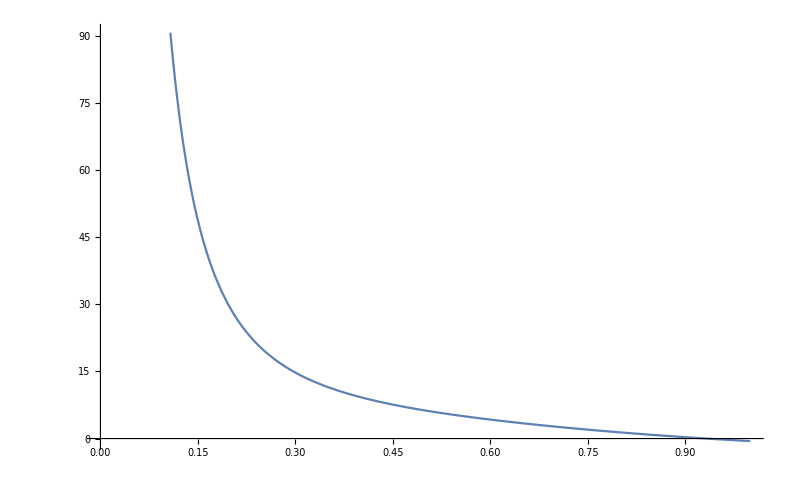

```mathematica
Plot[(Cos[a t]+a t Sin[a t])/(t)^2,{t,0,1}]
```

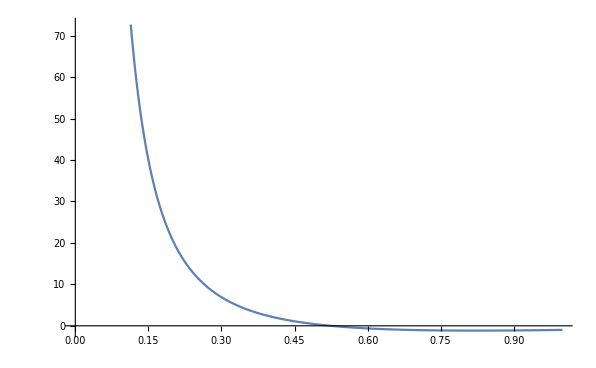

```mathematica
Plot[Cos[a t]/(t)^2,{t,0,1}]
```

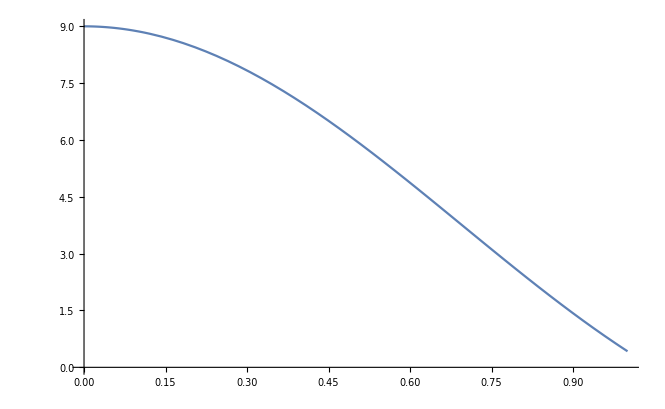

```mathematica
Plot[(a t Sin[a t])/(t)^2,{t,0,1}]
```

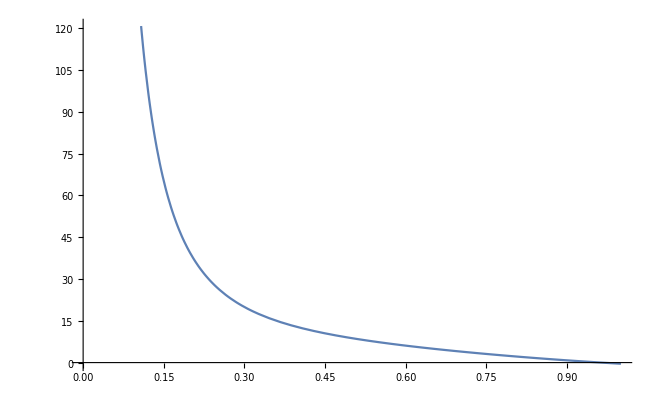

```mathematica
Plot[(a (1-t )Cos[a t]+(1+a^2 t)Sin[a t])/(a t)^2+(Cos[a t]+a t Sin[a t])/(t)^2,{t,0,1}]
```

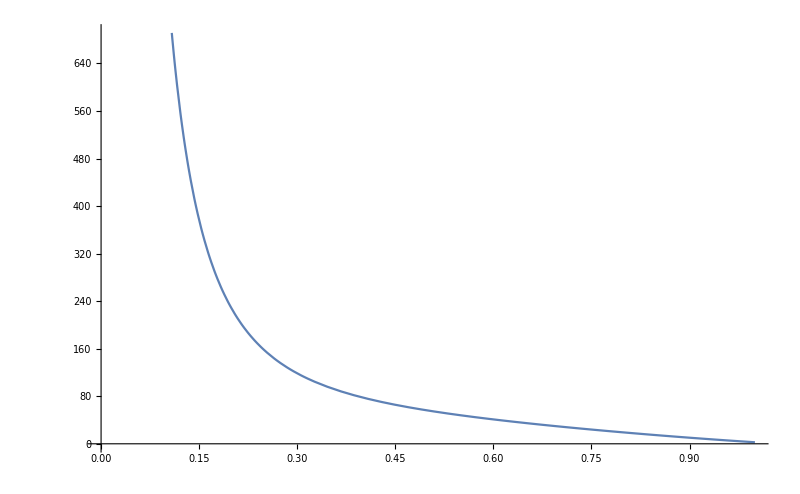

```mathematica
Plot[20(a (1-t )Cos[a t]+(1+a^2 t)Sin[a t])/(a t)^2+(Cos[a t]+a t Sin[a t])/(t)^2,{t,0,1}]
```